Underdamped 2

```mathematica
$Assumptions={τ>0,γ>0,ω0>0,√(-γ^2+4 ω0^2)>0,τR Re[s]>-1,τ>=t>=0,τ>=u>=0};
```

```mathematica
(* Relaxation function *)
```

```mathematica
Psi[t_]=ⅇ^(-γ Abs[t]) ((2 ω0^2)/(-γ^2+4 ω0^2)+((-γ^2+2 ω0^2) Cos[t √(-γ^2+4 ω0^2)])/(-γ^2+4 ω0^2)+(γ Sin[√(-γ^2+4 ω0^2) Abs[t]])/(√(-γ^2+4 ω0^2)));
dPsi[t_]=-(2 ⅇ^(-γ Abs[t]) γ ω0^2 Sign[t])/(-γ^2+4 ω0^2)+ⅇ^(-γ Abs[t]) γ Cos[t √(-γ^2+4 ω0^2)] Sign[t]+(ⅇ^(-γ Abs[t]) γ^3 Cos[t √(-γ^2+4 ω0^2)] Sign[t])/(-γ^2+4 ω0^2)-(2 ⅇ^(-γ Abs[t]) γ ω0^2 Cos[t √(-γ^2+4 ω0^2)] Sign[t])/(-γ^2+4 ω0^2)-(2 ⅇ^(-γ Abs[t]) ω0^2 Sin[t √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2));
ddPsi1[t_]=-2 ⅇ^(-γ Abs[t]) ω0^2 Cos[t √(-γ^2+4 ω0^2)]+(2 ⅇ^(-γ Abs[t]) γ^2 ω0^2)/(-γ^2+4 ω0^2)-ⅇ^(-γ Abs[t]) γ^2 Cos[t √(-γ^2+4 ω0^2)] -(ⅇ^(-γ Abs[t]) γ^4 Cos[t √(-γ^2+4 ω0^2)])/(-γ^2+4 ω0^2)+(2 ⅇ^(-γ Abs[t]) γ^2 ω0^2 Cos[t √(-γ^2+4 ω0^2)])/(-γ^2+4 ω0^2)-(ⅇ^(-γ Abs[t]) γ^3 Sign[t] Sin[t √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2))+(4 ⅇ^(-γ Abs[t]) γ ω0^2 Sign[t] Sin[t √(-γ^2+4 ω0^2)])/(√(-γ^2+4 ω0^2))-ⅇ^(-γ Abs[t]) γ √(-γ^2+4 ω0^2) Sign[t] Sin[t √(-γ^2+4 ω0^2)];
ddPsi2[t_]=-(4 ⅇ^(-γ Abs[t]) γ ω0^2)/(-γ^2+4 ω0^2)+2 ⅇ^(-γ Abs[t]) γ Cos[t √(-γ^2+4 ω0^2)]+(2 ⅇ^(-γ Abs[t]) γ^3 Cos[t √(-γ^2+4 ω0^2)])/(-γ^2+4 ω0^2)-(4 ⅇ^(-γ Abs[t]) γ ω0^2 Cos[t √(-γ^2+4 ω0^2)])/(-γ^2+4 ω0^2);
```

```mathematica
(* Dirac delta coefficients *)
```

```mathematica
f[s_]=-1/(s LaplaceTransform[ddPsi1[t]+ddPsi2[t]DiracDelta[t],t,s]);
```

```mathematica
c0=SeriesCoefficient[f[s],{s,0,0}];

c1=SeriesCoefficient[f[s],{s,0,1}];

c2=SeriesCoefficient[f[s],{s,0,2}];
```

```mathematica
(* Parameters and protocols *)
```

```mathematica
γ=1;
ω0=1;

τR=(γ^2+ω0^2)/(2 γ ω0^2);

g[t_]=(t+τR)/(τ+2τR);
h1[t_]=t/τ;
dh1[t_]=h1'[t];
h2[t_]=(t/τ)^2;
dh2[t_]=h2'[t];
h3[t_]=(t/τ)^3;
dh3[t_]=h3'[t];
```

```mathematica
(* Calculation of the irreversible work *)
```

```mathematica
W0[τ_]=Psi[0]/2+Integrate[dPsi[τ-t]g[t],{t,0,τ}]-1/2 Integrate[ddPsi1[t-u]g[t]g[u],{t,0,τ},{u,0,τ}]
```

1/2-(ⅇ^-τ (3 ⅇ^τ τ-√3 Sin[√3 τ]))/(3 (2+τ))+(ⅇ^-τ (3 ⅇ^τ+12 ⅇ^τ τ+6 ⅇ^τ τ^2-3 Cos[√3 τ]-5 √3 Sin[√3 τ]-4 √3 τ Sin[√3 τ]))/(12 (2+τ)^2)

```mathematica
W1[τ_]=W0[τ]+c0 dPsi[τ]/(τ+2τR)-c0/(τ+2τR)Integrate[ddPsi1[t]g[t],{t,0,τ}]+c0/(τ+2τR)Integrate[ddPsi1[τ-t]g[t],{t,0,τ}]-c0^2/(τ+2τR)^2 ddPsi1[0]+c0^2/(τ+2τR)^2 ddPsi1[τ]+c0/(τ+2τR)ddPsi2[τ]
```

1/2+1/(8 (2+τ)^2)+(2/3 ⅇ^(-Abs[τ])-8/3 ⅇ^(-Abs[τ]) Cos[√3 τ])/(16 (2+τ)^2)+(-4/3 ⅇ^(-Abs[τ])+4/3 ⅇ^(-Abs[τ]) Cos[√3 τ])/(4 (2+τ))-(ⅇ^-τ (3 ⅇ^τ τ-√3 Sin[√3 τ]))/(3 (2+τ))-(ⅇ^-τ (3 ⅇ^τ-3 Cos[√3 τ]+√3 Sin[√3 τ]))/(12 (2+τ)^2)+(-2/3 ⅇ^(-Abs[τ]) Sign[τ]+2/3 ⅇ^(-Abs[τ]) Cos[√3 τ] Sign[τ]-(2 ⅇ^(-Abs[τ]) Sin[√3 τ])/(√3))/(4 (2+τ))+(ⅇ^-τ (3 ⅇ^τ+12 ⅇ^τ τ+6 ⅇ^τ τ^2-3 Cos[√3 τ]-5 √3 Sin[√3 τ]-4 √3 τ Sin[√3 τ]))/(12 (2+τ)^2)-(ⅇ^-τ (-4+3 ⅇ^τ-2 τ+Cos[√3 τ]+2 τ Cos[√3 τ]-3 √3 Sin[√3 τ]-2 √3 τ Sin[√3 τ]))/(12 (2+τ)^2)

```mathematica
Wh1[τ_]=1/2 Integrate[Psi[t-u]dh1[t]dh1[u],{t,0,τ},{u,0,τ}]
```

(ⅇ^-τ (8-9 ⅇ^τ+12 ⅇ^τ τ+Cos[√3 τ]-√3 Sin[√3 τ]))/(12 τ^2)

```mathematica
Wh2[τ_]=1/2 Integrate[Psi[t-u]dh2[t]dh2[u],{t,0,τ},{u,0,τ}]
```

(ⅇ^-τ (-16+15 ⅇ^τ-16 τ-9 ⅇ^τ τ^2+8 ⅇ^τ τ^3+Cos[√3 τ]+τ Cos[√3 τ]+√3 τ Sin[√3 τ]))/(6 τ^4)

```mathematica
Wh3[τ_]=1/2 Integrate[Psi[t-u]dh3[t]dh3[u],{t,0,τ},{u,0,τ}]
```

1/(80 τ^6)3 ⅇ^-τ (640-645 ⅇ^τ+640 τ+320 τ^2+100 ⅇ^τ τ^3-90 ⅇ^τ τ^4+48 ⅇ^τ τ^5+5 Cos[√3 τ]-10 τ Cos[√3 τ]-20 τ^2 Cos[√3 τ]+5 √3 Sin[√3 τ]+10 √3 τ Sin[√3 τ])

```mathematica
(* Irreversible works *)
```

```mathematica
W0[τ_]=1/2-(ⅇ^-τ (3 ⅇ^τ τ-√3 Sin[√3 τ]))/(3 (2+τ))+(ⅇ^-τ (3 ⅇ^τ+12 ⅇ^τ τ+6 ⅇ^τ τ^2-3 Cos[√3 τ]-5 √3 Sin[√3 τ]-4 √3 τ Sin[√3 τ]))/(12 (2+τ)^2);

W1[τ_]=1/2+1/(8 (2+τ)^2)+(2/3 ⅇ^(-Abs[τ])-8/3 ⅇ^(-Abs[τ]) Cos[√3 τ])/(16 (2+τ)^2)+(-4/3 ⅇ^(-Abs[τ])+4/3 ⅇ^(-Abs[τ]) Cos[√3 τ])/(4 (2+τ))-(ⅇ^-τ (3 ⅇ^τ τ-√3 Sin[√3 τ]))/(3 (2+τ))-(ⅇ^-τ (3 ⅇ^τ-3 Cos[√3 τ]+√3 Sin[√3 τ]))/(12 (2+τ)^2)+(-2/3 ⅇ^(-Abs[τ]) Sign[τ]+2/3 ⅇ^(-Abs[τ]) Cos[√3 τ] Sign[τ]-(2 ⅇ^(-Abs[τ]) Sin[√3 τ])/(√3))/(4 (2+τ))+(ⅇ^-τ (3 ⅇ^τ+12 ⅇ^τ τ+6 ⅇ^τ τ^2-3 Cos[√3 τ]-5 √3 Sin[√3 τ]-4 √3 τ Sin[√3 τ]))/(12 (2+τ)^2)-(ⅇ^-τ (-4+3 ⅇ^τ-2 τ+Cos[√3 τ]+2 τ Cos[√3 τ]-3 √3 Sin[√3 τ]-2 √3 τ Sin[√3 τ]))/(12 (2+τ)^2);

Wh1[τ_]=(ⅇ^-τ (8-9 ⅇ^τ+12 ⅇ^τ τ+Cos[√3 τ]-√3 Sin[√3 τ]))/(12 τ^2);
Wh2[τ_]=(ⅇ^-τ (-16+15 ⅇ^τ-16 τ-9 ⅇ^τ τ^2+8 ⅇ^τ τ^3+Cos[√3 τ]+τ Cos[√3 τ]+√3 τ Sin[√3 τ]))/(6 τ^4);
Wh3[τ_]=1/(80 τ^6)3 ⅇ^-τ (640-645 ⅇ^τ+640 τ+320 τ^2+100 ⅇ^τ τ^3-90 ⅇ^τ τ^4+48 ⅇ^τ τ^5+5 Cos[√3 τ]-10 τ Cos[√3 τ]-20 τ^2 Cos[√3 τ]+5 √3 Sin[√3 τ]+10 √3 τ Sin[√3 τ]);
```

```mathematica
(* Plots *)
```

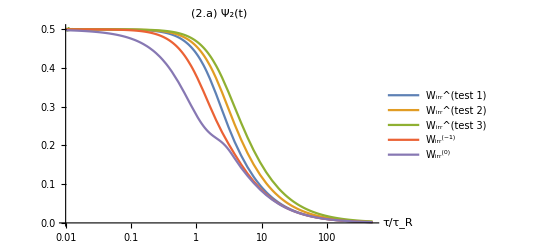

```mathematica
LogLinearPlot[{Legended[Wh1[τ],"W_irr^(test 1)"],Legended[Wh2[τ],"W_irr^(test 2)"],Legended[Wh3[τ],"W_irr^(test 3)"],Legended[W0[τ],"W_irr^(-1)"],Legended[W1[τ],"W_irr^(0)"]},{τ,0.01,500},PlotRange->Full,AxesLabel->{"τ/τ_R"},PlotLegends->Placed[{},{Right,Center}],PlotLabel->"(2.a) Ψ_2(t)"]
```

```mathematica
(* Error *)
```

```mathematica
ϵ1[τ_]= Abs[(W1[τ]-W0[τ])/W1[τ]];
```

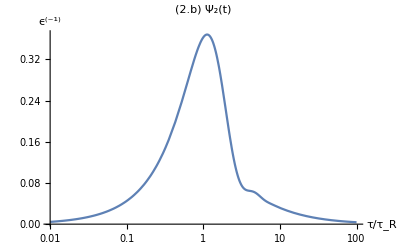

```mathematica
LogLinearPlot[ϵ1[τ],{τ,0.01,100},PlotRange->Full,AxesLabel->{"τ/τ_R","ϵ^(-1)"},PlotLabel->"(2.b) Ψ_2(t)"]
```